```mathematica
(*用于解pendulum问题的RungeKutta Algorithm *)
```

```mathematica
(*不含时*)
```

```mathematica
RKStep[f_,y_,yp_,h_]:=
Module[{k1,k2,k3,k4},k1=h*N[f/.Thread[y->yp]];
k2=h*N[f/.Thread[y->yp+k1/2]];
k3=h*N[f/.Thread[y->yp+k2/2]];
k4=h*N[f/.Thread[y->yp+k3]];
yp+(k1+2*k2+2*k3+k4)/6]
RungeK[f_,y_,y0_,{x_,dx_}]:=
NestList[RKStep[f,y,#,N[dx]]&,N[y0],Round[N[x/dx]]]
```

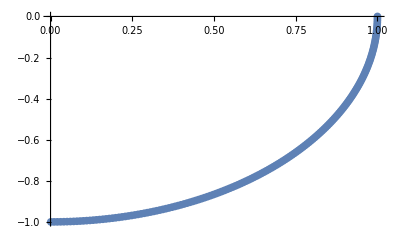

```mathematica
ListPlot[%]
```

```mathematica
(*上述x表示积分区间末端*)
```

```mathematica
(*含时*)
RKStepOverload[f_,y_,x_,xp_,yp_,h_]:=
Module[{k1,k2,k3,k4},k1=h*N[f/.Join[Flatten[{Thread[y->yp]}],{x->xp}]];
k2=h*N[f/.Join[Flatten[{Thread[y->yp+k1/2]}],{x->xp+h/2}] ];
k3=h*N[f/.Join[Flatten[{Thread[y->yp+k2/2]}],{x->xp+h/2}]];
k4=h*N[f/.Join[Flatten[{Thread[y->yp+k3]}],{x->xp+h}]];
  yp+(k1+2*k2+2*k3+k4)/6]
RungeKOverload[f_,y_,x_,y0_,{x0_,xe_,dx_}]:=Module[{tmpList={},i,yp=y0},
For[i=0,i<N[(xe-x0)/dx],i++,yp=RKStepOverload[f,y,x,x0+i*dx,yp,N[dx]];AppendTo[tmpList,yp]];tmpList]
```

```mathematica
(*解y''=x,y[0]=0的一个算例*)
```

```mathematica
RungeKOverload[{y1,x},{y,y1},x,{0,0},{0,1,0.01}]
```

```mathematica
g=9.8;l=0.4;r=0.1;w=70*2π/60;
```

```mathematica
RKStepOverload[{pθ,pφ,1/l(r w^2 Cos[θ] Cos[t w-φ]-g Sin[θ]+l Cos[θ] Sin[θ] pφ^2),(Csc[θ] (r w^2 Sin[t w-φ]-2 l Cos[θ]pθ pφ))/l},{θ,φ,pθ,pφ},t,0,{0.582,0,0.74,-1.42},0.005]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
lst=RungeKOverload[{pθ,pφ,1/l(r w^2 Cos[θ] Cos[t w-φ]-g Sin[θ]+l Cos[θ] Sin[θ] pφ^2),(Csc[θ] (r w^2 Sin[t w-φ]-2 l Cos[θ]pθ pφ))/l},{θ,φ,pθ,pφ},t,{ArcSin[0.711],3.14,0,w},{0,8,0.01}];
```

```mathematica
r*Cos[w t]-l*Sin[θ[t]]Cos[φ[t]],r*Sin[w t]-l*Sin[θ[t]]Sin[φ[t]]-l*Cos[θ[t]])
```

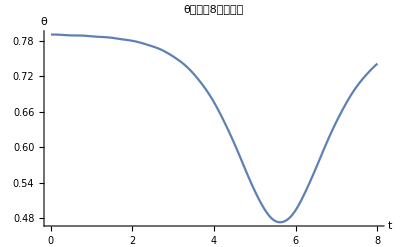

{7.93951,7.93903,7.93855,7.93808,7.93762,7.93716,7.93671,7.93628,7.93585,7.93544,7.93505,7.93467,7.9343,7.93395,7.93362,7.9333,7.933,7.93272,7.93245,7.9322,7.93196,7.93173,7.93152,7.93133,7.93114,7.93096,7.93079,7.93062,7.93047,7.93031,7.93016,7.93,7.92984,7.92968,7.92952,7.92934,7.92916,7.92897,7.92876,7.92855,7.92831,7.92807,7.9278,7.92752,7.92722,7.9269,7.92656,7.9262,7.92582,7.92543,7.92501,7.92457,7.92412,7.92365,7.92316,7.92265,7.92213,7.9216,7.92106,7.9205,7.91994,7.91937,7.91879,7.91821,7.91763,7.91704,7.91646,7.91588,7.9153,7.91473,7.91416,7.9136,7.91305,7.91251,7.91198,7.91146,7.91096,7.91047,7.90998,7.90952,7.90906,7.90862,7.90819,7.90777,7.90736,7.90696,7.90658,7.90619,7.90582,7.90545,7.90508,7.90472,7.90435,7.90399,7.90362,7.90324,7.90286,7.90247,7.90207,7.90166,7.90123,7.90079,7.90033,7.89986,7.89936,7.89885,7.89831,7.89775,7.89716,7.89656,7.89593,7.89527,7.89459,7.89389,7.89316,7.8924,7.89163,7.89083,7.89001,7.88917,7.88831,7.88744,7.88654,7.88563,7.88471,7.88377,7.88283,7.88187,7.88091,7.87994,7.87897,7.87799,7.87701,7.87603,7.87506,7.87408,7.87311,7.87214,7.87118,7.87022,7.86927,7.86832,7.86738,7.86645,7.86552,7.8646,7.86369,7.86278,7.86187,7.86096,7.86006,7.85916,7.85825,7.85735,7.85643,7.85552,7.85459,7.85365,7.85271,7.85175,7.85077,7.84978,7.84877,7.84774,7.84668,7.8456,7.8445,7.84337,7.84221,7.84102,7.8398,7.83854,7.83726,7.83594,7.83459,7.83321,7.83179,7.83034,7.82885,7.82734,7.82579,7.8242,7.82259,7.82095,7.81928,7.81758,7.81585,7.8141,7.81233,7.81053,7.80871,7.80687,7.80502,7.80315,7.80126,7.79936,7.79745,7.79552,7.79359,7.79165,7.78969,7.78774,7.78577,7.7838,7.78182,7.77983,7.77784,7.77585,7.77384,7.77183,7.76981,7.76778,7.76574,7.76369,7.76163,7.75955,7.75745,7.75534,7.75321,7.75106,7.74888,7.74668,7.74445,7.74219,7.7399,7.73758,7.73522,7.73282,7.73039,7.72791,7.72539,7.72283,7.72022,7.71757,7.71486,7.71211,7.70931,7.70645,7.70355,7.70059,7.69759,7.69453,7.69142,7.68826,7.68505,7.68178,7.67847,7.67511,7.67171,7.66825,7.66475,7.66121,7.65763,7.654,7.65033,7.64663,7.64288,7.6391,7.63529,7.63144,7.62756,7.62364,7.6197,7.61572,7.61172,7.60768,7.60362,7.59953,7.59541,7.59126,7.58708,7.58287,7.57863,7.57436,7.57005,7.56572,7.56134,7.55693,7.55248,7.548,7.54346,7.53889,7.53427,7.5296,7.52488,7.52011,7.51528,7.51039,7.50545,7.50044,7.49537,7.49024,7.48504,7.47976,7.47442,7.469,7.46351,7.45794,7.4523,7.44658,7.44077,7.43489,7.42893,7.42289,7.41677,7.41057,7.40428,7.39792,7.39147,7.38495,7.37835,7.37167,7.36492,7.35809,7.35119,7.34421,7.33716,7.33004,7.32285,7.31559,7.30827,7.30088,7.29343,7.28591,7.27833,7.27069,7.26298,7.25522,7.2474,7.23951,7.23157,7.22357,7.2155,7.20738,7.1992,7.19095,7.18264,7.17427,7.16584,7.15733,7.14876,7.14012,7.13141,7.12263,7.11377,7.10484,7.09582,7.08673,7.07755,7.06828,7.05893,7.04949,7.03995,7.03033,7.0206,7.01078,7.00086,6.99085,6.98072,6.9705,6.96017,6.94974,6.9392,6.92856,6.9178,6.90695,6.89598,6.88492,6.87374,6.86246,6.85108,6.8396,6.82801,6.81633,6.80454,6.79266,6.78069,6.76862,6.75646,6.74421,6.73187,6.71945,6.70694,6.69435,6.68169,6.66894,6.65612,6.64322,6.63026,6.61722,6.60411,6.59093,6.57768,6.56437,6.55099,6.53754,6.52403,6.51045,6.49681,6.4831,6.46932,6.45548,6.44157,6.4276,6.41356,6.39945,6.38526,6.37101,6.35669,6.34229,6.32782,6.31327,6.29865,6.28395,6.26918,6.25432,6.23939,6.22438,6.20929,6.19413,6.17888,6.16356,6.14815,6.13267,6.11712,6.10149,6.08579,6.07002,6.05418,6.03827,6.0223,6.00626,5.99017,5.97403,5.95783,5.94158,5.92529,5.90896,5.89259,5.87618,5.85975,5.84329,5.82682,5.81032,5.79381,5.77729,5.76077,5.74424,5.72772,5.7112,5.69469,5.67819,5.66171,5.64525,5.6288,5.61239,5.59599,5.57963,5.56329,5.54699,5.53072,5.51448,5.49828,5.48212,5.466,5.44992,5.43387,5.41787,5.40191,5.386,5.37013,5.3543,5.33852,5.32279,5.3071,5.29146,5.27587,5.26034,5.24486,5.22943,5.21407,5.19876,5.18351,5.16834,5.15323,5.13819,5.12323,5.10835,5.09355,5.07884,5.06422,5.04969,5.03527,5.02096,5.00676,4.99267,4.97871,4.96487,4.95117,4.93761,4.92418,4.91091,4.89779,4.88483,4.87203,4.8594,4.84694,4.83466,4.82256,4.81064,4.79891,4.78738,4.77603,4.76489,4.75394,4.7432,4.73266,4.72233,4.7122,4.70228,4.69257,4.68307,4.67378,4.6647,4.65583,4.64718,4.63873,4.6305,4.62247,4.61466,4.60706,4.59967,4.5925,4.58553,4.57878,4.57224,4.56591,4.5598,4.5539,4.54822,4.54276,4.53752,4.5325,4.5277,4.52313,4.51879,4.51467,4.51079,4.50715,4.50375,4.50058,4.49766,4.49499,4.49257,4.4904,4.48849,4.48683,4.48544,4.48431,4.48345,4.48286,4.48254,4.48248,4.4827,4.4832,4.48397,4.48501,4.48633,4.48792,4.48979,4.49193,4.49434,4.49703,4.49998,4.50319,4.50667,4.51042,4.51442,4.51867,4.52318,4.52793,4.53293,4.53817,4.54365,4.54936,4.55531,4.56148,4.56787,4.57448,4.58131,4.58835,4.5956,4.60306,4.61072,4.61859,4.62665,4.63491,4.64336,4.65201,4.66085,4.66988,4.6791,4.6885,4.69809,4.70787,4.71784,4.72799,4.73832,4.74884,4.75954,4.77043,4.78149,4.79274,4.80417,4.81578,4.82756,4.83953,4.85167,4.86399,4.87648,4.88914,4.90197,4.91496,4.92812,4.94144,4.95491,4.96854,4.98232,4.99625,5.01031,5.02452,5.03885,5.05332,5.0679,5.0826,5.09742,5.11234,5.12737,5.14249,5.1577,5.173,5.18838,5.20384,5.21936,5.23496,5.25061,5.26632,5.28208,5.29789,5.31375,5.32964,5.34558,5.36154,5.37754,5.39357,5.40962,5.42569,5.44179,5.45791,5.47405,5.4902,5.50637,5.52255,5.53875,5.55496,5.57118,5.58742,5.60366,5.61992,5.63618,5.65246,5.66874,5.68504,5.70134,5.71765,5.73396,5.75028,5.7666,5.78292,5.79924,5.81556,5.83188,5.84819,5.8645,5.88079,5.89708,5.91334,5.92959,5.94582,5.96202,5.9782,5.99434,6.01045,6.02652,6.04255,6.05853,6.07447,6.09035,6.10617,6.12194,6.13765,6.15328,6.16885,6.18435,6.19977,6.21512,6.23038,6.24557,6.26067,6.27568,6.29061,6.30545,6.3202,6.33486,6.34943,6.36391,6.37829,6.39259,6.40679,6.4209,6.43493,6.44886,6.46271,6.47646,6.49014,6.50372,6.51723,6.53065,6.54399,6.55725,6.57043,6.58353,6.59656,6.60951,6.62239,6.6352,6.64793,6.66059,6.67319,6.68571,6.69816,6.71054,6.72285,6.73509,6.74726,6.75936,6.77139,6.78334,6.79522,6.80703,6.81875,6.8304,6.84197,6.85346,6.86487,6.87619,6.88743,6.89858,6.90964,6.9206,6.93148,6.94226,6.95294,6.96353,6.97402,6.98441,6.9947,7.00489,7.01497,7.02495,7.03483,7.04461,7.05428,7.06385,7.07331,7.08268,7.09194,7.1011,7.11017,7.11913,7.128,7.13678,7.14546,7.15405,7.16255,7.17096,7.17929,7.18754,7.1957,7.20379,7.2118,7.21974,7.2276,7.2354,7.24312,7.25079,7.25838,7.26592,7.27339,7.28081}

```mathematica
ListLinePlot[Transpose[{Table[i,{i,0.01,8,0.01}],lst[[start;;end,1]]}],AxesLabel->{"t","θ"},PlotLabel->"θ角在前8秒的变化"]
```

```mathematica
Length[Table[i,{i,35.005,40,0.005}]]
```

1000

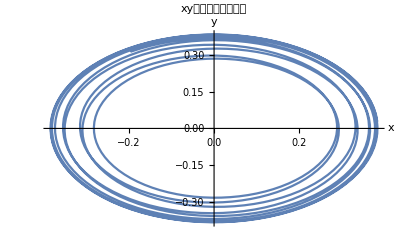

```mathematica
g=9.8;l=0.4;r=0.1;w=70*2π/60;
start=1;end=800;tStart=0.01;tEnd=8;tDelta=0.01;
x=r*Cos[w t]-l*Sin[θ]Cos[φ]/.{θ->lst[[start;;end,1]],φ->lst[[start;;end,2]],t->Table[i,{i,tStart,tEnd,tDelta}]};
y=r*Sin[w t]-l*Sin[θ]Sin[φ]/.{θ->lst[[start;;end,1]],φ->lst[[start;;end,2]],t->Table[i,{i,tStart,tEnd,tDelta}]};vx=-r w Sin[t w]-l Cos[θ] Cos[φ] pθ+l Sin[θ] Sin[φ]pφ/.{θ->lst[[start;;end,1]],φ->lst[[start;;end,2]], pθ->lst[[start;;end,3]],pφ->lst[[start;;end,4]],t->Table[i,{i,tStart,tEnd,tDelta}]};
vy=r w Cos[t w]-l Cos[θ] Sin[φ] pθ-l Cos[φ] Sin[θ] pφ/.{θ->lst[[start;;end,1]],φ->lst[[start;;end,2]], pθ->lst[[start;;end,3]],pφ->lst[[start;;end,4]],t->Table[i,{i,tStart,tEnd,tDelta}]};
ListLinePlot[Transpose[{x,y}],AxesLabel->{"x","y"},PlotLabel->"xy平面小球运动轨迹"]
```

```mathematica
vx[[1]]
```

-0.203054

```mathematica
vy[[1]]
```

2.81039

```mathematica
Clear[r,l,w]
D[r*Sin[w t]-l*Sin[θ[t]]Sin[φ[t]],t]
```

r w Cos[t w]-l Cos[θ[t]] Sin[φ[t]] θ'[t]-l Cos[φ[t]] Sin[θ[t]] φ'[t]

```mathematica
-r w Sin[t w]-l Cos[θ] Cos[φ] pθ+l Sin[θ] Sin[φ]pφ
```

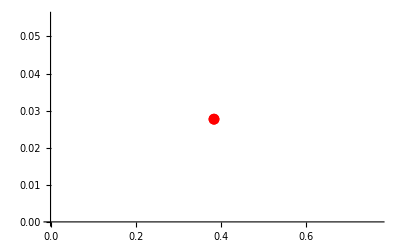

```mathematica
ListPlot[{{x[[1]],y[[1]]}},PlotStyle->{Red}]
```

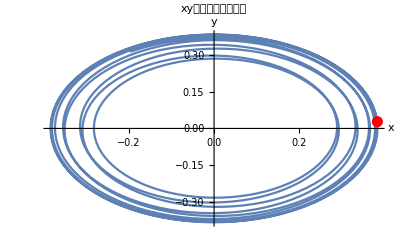

```mathematica
Show[%94,%99,PlotRange->All]
```

```mathematica
x[[200]]
```

-0.158846

```mathematica
x[[501]]
```

```mathematica
x[[200]]
```

0.239495

```mathematica
x[[1]]
```

-0.125887

-0.339109

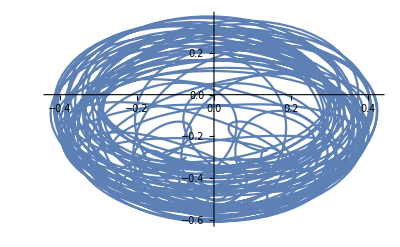

```mathematica
y[[1]]
```

4000

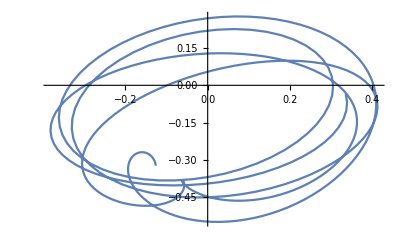

```mathematica
Length[lst[[;;,1]]]
```

```mathematica
t+φ/.{t->{1,2},φ->
```

{1,2}

{{1.00677,-0.0141137,0.614502,-1.40085},{1.01228,-0.0279798,0.486594,-1.37053},{1.0165,-0.0414877,0.355955,-1.32924},{1.01939,-0.0545289,0.222301,-1.27725},{1.02093,-0.066998,0.0853932,-1.21487},{1.02109,-0.0787928,-0.0549648,-1.14245},{1.01982,-0.0898147,-0.198925,-1.06035},{1.0171,-0.0999688,-0.346597,-0.96894},{1.01288,-0.109164,-0.498045,-0.868589},{1.00712,-0.117312,-0.65329,-0.759632},{0.999798,-0.124329,-0.812311,-0.642359},{0.990864,-0.130132,-0.975042,-0.516987},{0.980285,-0.134642,-1.14137,-0.383633},{0.968025,-0.137778,-1.31114,-0.242281},{0.954052,-0.13946,-1.48412,-0.0927442},{0.938333,-0.139604,-1.66006,0.0653796},{0.920842,-0.138122,-1.8386,0.232764},{0.901554,-0.134915,-2.01933,0.410423},{0.88045,-0.129874,-2.20172,0.599798},{0.857516,-0.122873,-2.38513,0.802874},{0.832746,-0.113762,-2.56879,1.02233},{0.806143,-0.102361,-2.75173,1.26173},{0.777718,-0.0884457,-2.93277,1.52582},{0.747498,-0.0717411,-3.11043,1.8209},{0.715527,-0.0518969,-3.28282,2.15535},{0.681867,-0.028466,-3.44754,2.5404},{0.646612,-0.000870598,-3.60147,2.99118},{0.609888,0.0316444,-3.74045,3.5283},{0.571871,0.0700759,-3.85885,4.17997},{0.532805,0.115753,-3.94886,4.98504},{0.493025,0.170463,-3.99939,5.99687},{0.453001,0.236618,-3.99438,7.2876},{0.413399,0.317454,-3.91028,8.95028},{0.375172,0.417221,-3.71268,11.0908},{0.339683,0.541151,-3.35312,13.7891},{0.308852,0.694737,-2.77057,16.9908},{0.28521,0.88142,-1.90871,20.3013},{0.271645,1.09818,-0.762071,22.8254},{0.270602,1.33163,0.568864,23.4991},{0.282999,1.5607,1.89244,21.9995},{0.307832,1.76685,3.03549,19.0931},{0.342856,1.94154,3.92746,15.8603},{0.38559,2.08529,4.58409,12.9723},{0.433913,2.20289,5.05364,10.6427},{0.486198,2.29993,5.38353,8.84686},{0.541241,2.38128,5.61016,7.48563},{0.598144,2.45075,5.75917,6.45726},{0.656225,2.51125,5.84808,5.67856},{0.714946,2.56495,5.88899,5.0868},{0.773873,2.61346,5.8904,4.63615},{0.832643,2.65803,5.8585,4.29341},{0.890948,2.69961,5.79796,4.03449},{0.948519,2.73894,5.71248,3.8418},{1.00512,2.77662,5.60506,3.70235},{1.06056,2.81313,5.47826,3.60649},{1.11463,2.84887,5.33429,3.54693},{1.16719,2.88417,5.17511,3.5181},{1.21809,2.91932,5.00243,3.5157},{1.2672,2.95456,4.81782,3.53634},{1.31441,2.99011,4.62261,3.5773},{1.35962,3.02617,4.41802,3.63634},{1.40274,3.0629,4.20506,3.71157},{1.4437,3.10045,3.98461,3.80134},{1.48241,3.13897,3.75737,3.90414},{1.51882,3.17857,3.52392,4.01856},{1.55287,3.21937,3.2847,4.14322},{1.5845,3.26146,3.04001,4.27675},{1.61365,3.30493,2.79008,4.41773},{1.64028,3.34984,2.53504,4.56473},{1.66434,3.39624,2.27497,4.71623},{1.68577,3.44417,2.00993,4.87069},{1.70452,3.49366,1.73997,5.02653},{1.72055,3.5447,1.46515,5.18217},{1.73381,3.5973,1.18563,5.33605},{1.74425,3.65141,0.901599,5.4867},{1.75183,3.70701,0.613371,5.63277},{1.7565,3.76405,0.321372,5.77312},{1.75824,3.82245,0.0261539,5.90684},{1.75702,3.88216,-0.271592,6.03335},{1.75281,3.9431,-0.57104,6.15241},{1.74559,4.00519,-0.871227,6.2642},{1.73538,4.06836,-1.17106,6.36931},{1.72218,4.13255,-1.46933,6.46882},{1.706,4.19772,-1.7647,6.56419},{1.6869,4.26383,-2.05572,6.65739},{1.66491,4.33087,-2.34084,6.75074},{1.64011,4.39885,-2.61835,6.847},{1.61257,4.46783,-2.88642,6.94929},{1.58242,4.53787,-3.14303,7.06107},{1.54976,4.6091,-3.38593,7.18614},{1.51475,4.68165,-3.6126,7.32863},{1.47757,4.75574,-3.82017,7.493},{1.43842,4.8316,-4.00535,7.684},{1.39755,4.90953,-4.16431,7.9067},{1.35524,4.98986,-4.29258,8.1664},{1.31182,5.073,-4.38496,8.46851},{1.26768,5.15939,-4.43537,8.81834},{1.22328,5.24954,-4.43681,9.22066},{1.17913,5.34399,-4.3813,9.67908},{1.13587,5.44331,-4.25997,10.195}}

```mathematica
alpha=0.4;Omega=10π;u=0.2;beta=0;R=0.05;g=9.8;theta=0*π/180;
f[x_,y_,vx_,vy_,wx_,wy_]:=Sqrt[(vx-R*wy+Omega*y)^2+(vy+R*wx-Omega*x)^2];
f1[x_,y_,vx_,vy_,wx_,wy_]:=(vx-R*wy+Omega*y)/f[x,y,vx,vy,wx,wy];
f2[x_,y_,vx_,vy_,wx_,wy_]:=(vy+R*wx-Omega*x)/f[x,y,vx,vy,wx,wy];
f3[wx_,wy_]:=Sqrt[wx^2+wy^2]+N[10^(-10)];
```

```mathematica
f
```

f

```mathematica
f[1,1,1,1,1,1]
```

14.1423

```mathematica
f1[1,1,1,1,1]
```

10.95/(√(119.902+(-9+0.05 wx)^2))

```mathematica
f3[1,1]
```

1.41421

```mathematica
f3[0,0]
```

1.×10^-10

```mathematica
f2[1,1,1,1]
```

0.874157

```mathematica
Norm[{wx,wy}]
```

√(Abs[wx]^2+Abs[wy]^2)

```mathematica
lst=RungeKOverload[{vx,vy,-u*g*f1[x,y,vx,vy,wx,wy],g*Sin[theta]-u*g*f2[x,y,vx,vy,wx,wy],(-1*u*f2[x,y,vx,vy,wx,wy]-beta*wx/f3[wx,wy])*g/(alpha*R),(-1*u*f1[x,y,vx,vy,wx,wy]-beta*wy/f3[wx,wy])*g/(alpha*R)},{x,y,vx,vy,wx,wy},t,{0.05,0,-0.107,0,0.01,0.01},{0,4,0.003}];
```

```mathematica
lst1=RungeK[{vx,vy,-u*g*f1[x,y,vx,vy,wy],g*Sin[theta]-u*g*f2[x,y,vx,vy,wx],(-1*u*f2[x,y,vx,vy,wx]-beta*wx/f3[wx,wy])*g/(alpha*R),(-1*u*f1[x,y,vx,vy,wx]-beta*wy/f3[wx,wy])*g/(alpha*R)},{x,y,vx,vy,wx,wy},{0.05,0,-0.107,0,0.01,0.01},{0.5,0.05}];
```

```mathematica
lst
```

$Aborted[]

```mathematica
Length[lst]
```

200

```mathematica
lst[[200]]
```

{0.0618323,0.497612,-0.11979,0.989893}

```mathematica
Length[Range[0,0.995,0.005]]
```

200

```mathematica
lst[[1]]
```

{0.1,0.0000125,-1.91571×10^-7,0.005}

```mathematica
(alpha+1)/alpha lst[[;;,3]]-Omega*lst[[;;,2]]
```

```mathematica
Length[lst]
```

400

```mathematica
Length[Table[i,{i,0.01,4,0.01}]]
```

400

```mathematica
Length[Cos@lst[[;;,2]]//N]
```

400

```mathematica
lst[[1,2]]
```

0.000228979

```mathematica
ListLinePlot[Transpose[{x,y}]]
```

-Graphics-

```mathematica
x
```

{-0.126113,-0.126813,-0.12795,-0.129512,-0.131483,-0.133841,-0.136561,-0.139614,-0.142963,-0.146571,-0.150393,-0.154382,-0.158486,-0.162649,-0.166812,-0.170911,-0.174881,-0.178653,-0.182156,-0.185318,-0.188065,-0.190321,-0.192014,-0.193068,-0.193413,-0.192979,-0.1917,-0.189513,-0.186363,-0.182199,-0.176976,-0.17066,-0.163223,-0.154647,-0.144925,-0.134059,-0.122062,-0.108959,-0.0947839,-0.0795835,-0.0634132,-0.0463389,-0.028435,-0.00978447,0.00952295,0.0293913,0.0497198,0.0704039,0.0913363,0.112408,0.133511,0.154534,0.175371,0.195915,0.216062,0.235711,0.254762,0.273121,0.290693,0.307388,0.323118,0.337796,0.35134,0.363665,0.374693,0.384343,0.392538,0.399202,0.404261,0.40764,0.409272,0.409089,0.407027,0.403029,0.397041,0.389017,0.378921,0.366724,0.352409,0.335973,0.317427,0.296799,0.274134,0.249498,0.222979,0.194689,0.164765,0.133368,0.100689,0.0669436,0.0323777,-0.00273779,-0.0381055,-0.0734042,-0.108291,-0.142407,-0.175376,-0.206815,-0.236338,-0.263562,-0.288113,-0.309634,-0.327793,-0.34229,-0.352864,-0.359301,-0.361439,-0.359173,-0.35246,-0.341325,-0.325857,-0.306215,-0.282622,-0.25537,-0.224807,-0.191339,-0.155425,-0.117563,-0.0782905,-0.0381718,0.00220838,0.042254,0.0813663,0.118952,0.154434,0.187256,0.216894,0.242865,0.264732,0.282113,0.294692,0.302219,0.304522,0.301511,0.293183,0.279625,0.261017,0.23763,0.20983,0.178067,0.142876,0.104863,0.0646993,0.0231041,-0.0191677,-0.061343,-0.102648,-0.142324,-0.17965,-0.213955,-0.244635,-0.271167,-0.293119,-0.310157,-0.322052,-0.328679,-0.330017,-0.326142,-0.317223,-0.303511,-0.285328,-0.263056,-0.237125,-0.207998,-0.176164,-0.142122,-0.106371,-0.0694041,-0.0316983,0.00629203,0.0441396,0.0814481,0.117855,0.153035,0.186694,0.21858,0.24847,0.27618,0.301553,0.324465,0.344819,0.362542,0.377586,0.389924,0.399546,0.406461,0.410693,0.412279,0.41127,0.407726,0.401721,0.393337,0.382666,0.369808,0.354875,0.337983,0.319261,0.298845,0.276878,0.253512,0.228908,0.203231,0.176657,0.149363,0.121534,0.0933563,0.0650185,0.0367095,0.00861647,-0.019077,-0.0461928,-0.0725602,-0.0980178,-0.122415,-0.145615,-0.167493,-0.187941,-0.206868,-0.224198,-0.239873,-0.253853,-0.266113,-0.276646,-0.285461,-0.292581,-0.298043,-0.301897,-0.304203,-0.305032,-0.304463,-0.302582,-0.29948,-0.295254,-0.290001,-0.283823,-0.276821,-0.269096,-0.260749,-0.251877,-0.242577,-0.232941,-0.223057,-0.213011,-0.202883,-0.192749,-0.182679,-0.172739,-0.162991,-0.153489,-0.144284,-0.135421,-0.126942,-0.11888,-0.111266,-0.104125,-0.0974779,-0.0913403,-0.0857233,-0.0806333,-0.0760722,-0.0720375,-0.0685224,-0.0655157,-0.0630018,-0.0609611,-0.05937,-0.0582005,-0.0574211,-0.0569965,-0.0568877,-0.0570523,-0.057445,-0.0580173,-0.0587183,-0.0594947,-0.0602914,-0.0610519,-0.0617186,-0.0622332,-0.0625376,-0.0625739,-0.0622857,-0.0616177,-0.0605172,-0.0589342,-0.0568219,-0.0541376,-0.0508432,-0.0469053,-0.0422963,-0.0369944,-0.0309838,-0.0242556,-0.0168073,-0.00864344,0.000224874,0.00977964,0.0199964,0.0308443,0.0422867,0.0542815,0.0667815,0.0797351,0.0930866,0.106777,0.120745,0.134927,0.149257,0.163667,0.178091,0.192459,0.206703,0.220754,0.234543,0.248,0.261056,0.273643,0.285691,0.297129,0.307889,0.3179,0.32709,0.33539,0.342727,0.349031,0.35423,0.358252,0.361029,0.36249,0.36257,0.361203,0.358329,0.353891,0.347839,0.340126,0.330716,0.319579,0.306697,0.292061,0.275677,0.257563,0.237753,0.216296,0.193259,0.168726,0.142801,0.115607,0.0872846,0.0579951,0.0279179,-0.00274994,-0.0337948,-0.0649881,-0.0960884,-0.126844,-0.156995,-0.186277,-0.214424,-0.241172,-0.266261,-0.289443,-0.310478,-0.329145,-0.34524,-0.35858,-0.369006,-0.376385,-0.380612,-0.381611,-0.379333,-0.373762,-0.364911,-0.352823,-0.337573,-0.319262,-0.298022,-0.274014,-0.247425,-0.218469,-0.187386,-0.154443,-0.119929,-0.0841594,-0.0474711,-0.0102233,0.0272042,0.0644129,0.100988,0.136499,0.170509,0.202571,0.232239,0.259071,0.282641,0.302537,0.318382,0.329835,0.336603,0.338456,0.335229}

```mathematica
y
```

$Aborted[]

```mathematica
lst[[;;,4]]
```

{0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.0399999,0.0449999,0.0499998,0.0549997,0.0599995,0.0649994,0.0699991,0.0749989,0.0799985,0.0849982,0.0899977,0.0949972,0.0999965,0.104996,0.109995,0.114994,0.119993,0.124992,0.129991,0.134989,0.139988,0.144986,0.149984,0.154982,0.15998,0.164978,0.169975,0.174972,0.179969,0.184966,0.189963,0.194959,0.199955,0.204951,0.209946,0.214942,0.219937,0.224931,0.229926,0.23492,0.239914,0.244907,0.249901,0.254894,0.259886,0.264878,0.26987,0.274861,0.279852,0.284843,0.289833,0.294823,0.299813,0.304802,0.30979,0.314778,0.319766,0.324753,0.32974,0.334726,0.339712,0.344697,0.349682,0.354666,0.35965,0.364633,0.369615,0.374597,0.379579,0.38456,0.38954,0.39452,0.399499,0.404477,0.409455,0.414433,0.419409,0.424385,0.42936,0.434335,0.439309,0.444282,0.449255,0.454227,0.459198,0.464169,0.469138,0.474107,0.479076,0.484043,0.48901,0.493976,0.498941,0.503905,0.508869,0.513831,0.518793,0.523754,0.528715,0.533674,0.538632,0.54359,0.548547,0.553503,0.558458,0.563412,0.568365,0.573317,0.578268,0.583219,0.588168,0.593117,0.598064,0.603011,0.607956,0.6129,0.617844,0.622786,0.627728,0.632668,0.637608,0.642546,0.647483,0.652419,0.657354,0.662288,0.667221,0.672153,0.677083,0.682013,0.686941,0.691868,0.696794,0.701719,0.706643,0.711565,0.716487,0.721407,0.726326,0.731244,0.73616,0.741075,0.745989,0.750902,0.755813,0.760723,0.765632,0.77054,0.775446,0.780351,0.785255,0.790157,0.795058,0.799958,0.804856,0.809753,0.814648,0.819542,0.824435,0.829326,0.834216,0.839105,0.843992,0.848877,0.853762,0.858644,0.863525,0.868405,0.873283,0.87816,0.883036,0.887909,0.892782,0.897652,0.902521,0.907389,0.912255,0.91712,0.921983,0.926844,0.931704,0.936562,0.941418,0.946273,0.951127,0.955978,0.960828,0.965677,0.970523,0.975368,0.980212,0.985053,0.989893}

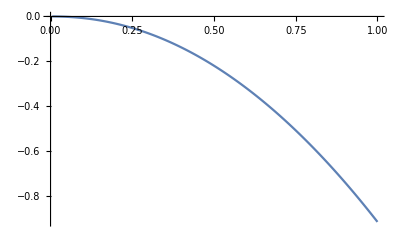

```mathematica
ListLinePlot[Transpose[{Range[0.005,1,0.005],(alpha+1)/alpha lst[[;;,3]]-Omega*lst[[;;,2]]}]]
```

```mathematica
(*求解一种稳定的情况,φ[t]=t,r=1/2,l=√2/2,w=g=1,θ[0]=π/4,θ'=0]*)
```

```mathematica
RungeKOverload[{pθ,pφ,√2(1/2  Cos[θ] Cos[t-φ]-Sin[θ]+(√2)/2 Cos[θ] Sin[θ] (pφ)^2),√2 Csc[θ] (1/2 Sin[t-φ]-√2 Cos[θ]pθ pφ)},{θ,φ,pθ,pφ},t,{π/4,0,0,1},{0,2π,0.01}]
```